# Production Runs – Exciton & Biexciton Energies

Final energy evaluations for the paper (semi-ellipsoidal QD analog of the reference: Non-Linear Optical Properties of Biexciton in Ellipsoidal Quantum Dot, Nanomaterials 12, 1412). States follow the paper's notation: exciton |ij> = e_i h_j, biexciton |ijkl> = e_i e_j h_k h_l, with level 0 = {1,0,0} and level 1 = {1,0,1} (first in-plane excitation). Six geometries (in effective Bohr radii; 1 rB ~ 10 nm for GaAs): the base point (5, 0.5) ~ (50 nm, 5 nm), the small-semiaxis scan c = 0.5 / 0.55 / 0.6 at a = 5, c = 1.0 for the second energy-diagram set, and a = 4 / 6 at c = 0.5 for the large-semiaxis dependence.

Every run follows the validated protocol from the Computational Design Log: minimize (warm-started when the configuration was seen before), re-evaluate the energy at the optimum with the production budget, stamp with the quadrature identity checks. Results are checkpointed to production-results.wxf after every run, so the notebook can be aborted and resumed freely; completed runs are skipped on re-evaluation. Distinct-orbital biexciton configurations automatically get the larger budgets (see the validation table in the log note).

Evaluate top to bottom; the per-geometry sections are independent and can be run in any order or on different days.

## Load both frameworks

```mathematica
dir = NotebookDirectory[];
Get[FileNameJoin[{ParentDirectory[dir, 3], "shared", "numerics", "definitions.wl"}]];
exDir = FileNameJoin[{ParentDirectory[dir, 2], "exciton", "01-numerics"}];
Get[FileNameJoin[{exDir, "mixed-correlation.wl"}]];
Get[FileNameJoin[{exDir, "mixed-density.wl"}]];
Get[FileNameJoin[{exDir, "mixed-integrals.wl"}]];
Get[FileNameJoin[{dir, "mixed-correlation.wl"}]];
Get[FileNameJoin[{dir, "mixed-density.wl"}]];
Get[FileNameJoin[{dir, "mixed-integrals.wl"}]];
```

```mathematica
(* smoke test: exact identity, must be ~1 to ~0.1% *)
normExciton[5.0, 0.5, 0.]
```

0.999998

## Result store and protocol runners

```mathematica
(* checkpointed result store; completed runs are skipped *)
prodFile = FileNameJoin[{dir, "production-results.wxf"}];
prodResults = If[FileExistsQ[prodFile], Import[prodFile, "WXF"], <||>];
prodSave[] := Export[prodFile, prodResults, "WXF"];
prodKey[label_, aa_, cc_] :=
  StringJoin[label, "|a=", ToString[aa], "|c=", ToString[cc]];
```

```mathematica
(* exciton protocol: minimize (fast, 5-dim integrals) -> re-evaluate at the
   optimum with 10^6 points -> identity stamp. *)
runExciton[label_, aa_, cc_, eState_, hState_] :=
  Module[{key = prodKey[label, aa, cc], opt, al, res},
   If[KeyExistsQ[prodResults, key], Return[prodResults[key]]];
   exElectronState = eState; exHoleState = hState;
   minimizeExciton[aa, cc];
   opt = exOptimum[]; al = opt["params"][[1]];
   res = Block[{exMaxPoints = 10^6},
     Append[totalEnergyExciton[aa, cc, al],
      <|"alpha" -> al, "label" -> label,
        "check" -> exQuadratureCheck[aa, cc, al]|>]];
   prodResults[key] = res; prodSave[]; res];
```

```mathematica
(* biexciton protocol: distinct-orbital configurations get 4-5x budgets
   (interference partially cancels the density; see the Design Log table).
   start: Automatic uses the per-configuration archive; pass the params of a
   neighbouring geometry to seed a scan. *)
runBiexciton[label_, aa_, cc_, eStates_, hStates_, etaE_, etaH_,
   start_: Automatic] :=
  Module[{key = prodKey[label, aa, cc], distinct, minPts, finPts, opt, p, res},
   If[KeyExistsQ[prodResults, key], Return[prodResults[key]]];
   bxElectronStates = eStates; bxHoleStates = hStates;
   bxEtaE = etaE; bxEtaH = etaH;
   distinct = (eStates[[1]] =!= eStates[[2]]) || (hStates[[1]] =!= hStates[[2]]);
   minPts = If[distinct, 10^6, 2*10^5];
   finPts = If[distinct, 4*10^6, 10^6];
   Block[{bxMaxPoints = minPts}, minimizeBiexciton[aa, cc, 50, start]];
   opt = bxOptimum[]; p = opt["params"];
   res = Block[{bxMaxPoints = finPts, bxPrecisionGoal = 3},
     Append[totalEnergyBiexciton[aa, cc, Sequence @@ p],
      <|"params" -> p, "label" -> label,
        "evaluations" -> opt["evaluations"],
        "check" -> bxQuadratureCheckAll[aa, cc, Sequence @@ p]|>]];
   prodResults[key] = res; prodSave[]; res];
```

```mathematica
(* worst identity spread of a stored run -- quick health readout *)
worstSpread[res_] := Max[Cases[res["check"],
    KeyValuePattern["relSpread" -> s_] :> s, {1}]];
```

## Configurations

```mathematica
(* particle levels: 0 = ground, 1 = first in-plane excitation *)
lvl[0] = {1, 0, 0}; lvl[1] = {1, 0, 1};

(* states per geometry: 3 exciton + 3 biexciton (paper's Figure 2 scheme).
   |0010> = one hole excited (first XX excitation: the hole is heavier);
   |1000> = one electron excited. Spatially symmetric (spin-singlet) pairs. *)
runAllStates[aa_, cc_] :=
  Module[{seed},
   runExciton["X00", aa, cc, lvl[0], lvl[0]];
   runExciton["X01", aa, cc, lvl[0], lvl[1]];
   runExciton["X10", aa, cc, lvl[1], lvl[0]];
   (* seed each biexciton run from the same geometry's ground-config optimum *)
   seed = runBiexciton["XX0000", aa, cc,
      {lvl[0], lvl[0]}, {lvl[0], lvl[0]}, 1, 1]["params"];
   runBiexciton["XX0010", aa, cc,
    {lvl[0], lvl[0]}, {lvl[0], lvl[1]}, 1, 1, seed];
   runBiexciton["XX1000", aa, cc,
    {lvl[0], lvl[1]}, {lvl[0], lvl[0]}, 1, 1, seed];
   Dataset[KeySelect[prodResults,
     StringContainsQ[#, prodKey["", aa, cc]] &]]];

(* geometry grid, in rB:
   (5, 0.5)  base point  (~50 nm, 5 nm)  -- transition diagram, chi3;
   (5, 0.55), (5, 0.6)   small-semiaxis scan (Figs. 4, 6 analogs);
   (5, 1.0)              second energy-diagram set (Fig. 1 analog);
   (4, 0.5), (6, 0.5)    large-semiaxis dependence. *)
geometries = {{5.0, 0.5}, {5.0, 0.55}, {5.0, 0.6},
   {5.0, 1.0}, {4.0, 0.5}, {6.0, 0.5}};
```

## Production runs (one cell per geometry; each is resumable)

```mathematica
runAllStates[5.0, 0.5]
```

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.872748 and 0.00196475 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0.166395 and 0.000202484 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

```mathematica
dir="C:/Users/davit/Documents/PhD/projects/biexciton/01-numerics";
prodResults=Import[FileNameJoin[{dir,"production-results.wxf"}],"WXF"];
Dataset[prodResults,MaxItems->{All,All,All}]
```

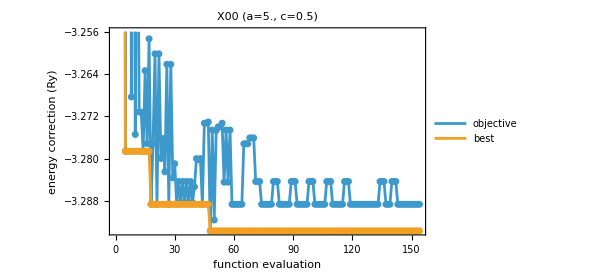
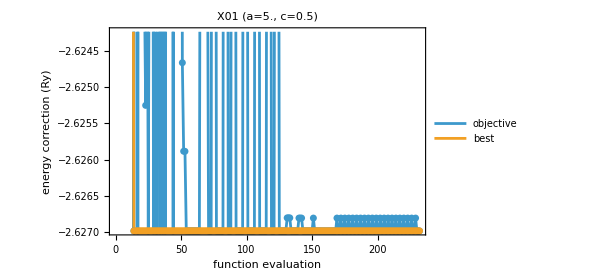
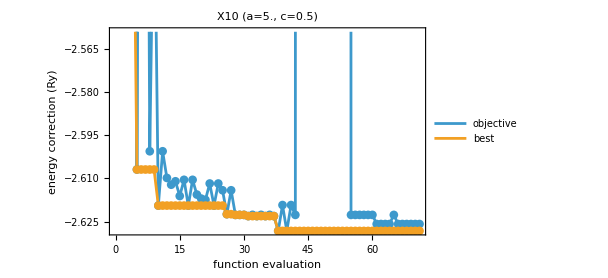

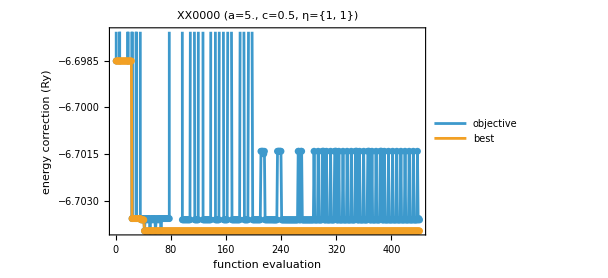
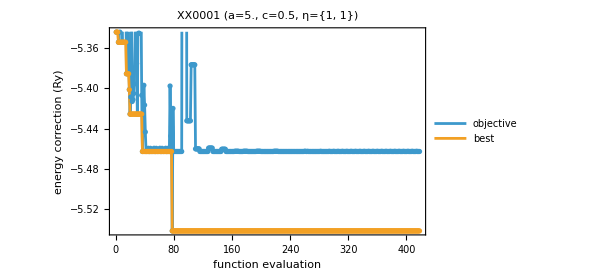
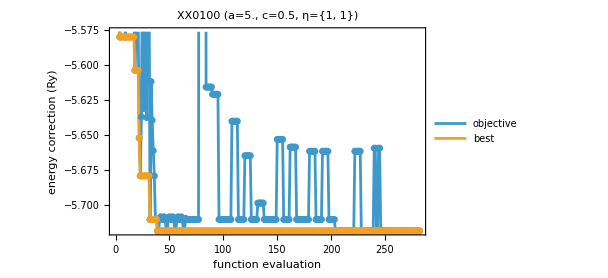

```mathematica
exRunArchive=Import[exArchiveFile,"WXF"];
bxRunArchive=Import[bxArchiveFile,"WXF"];

lvlIndex[s_]:=s/. {{1,0,0}->0,{1,0,1}->1,{1,0,2}->2};
exLabel[key_]:="X"<>StringJoin[ToString/@(lvlIndex/@{key["electronState"],key["holeState"]})]<>"   (a="<>ToString[key["a"]]<>", c="<>ToString[key["c"]]<>")";
bxLabel[key_]:="XX"<>StringJoin[ToString/@(lvlIndex/@Join[key["electronStates"],key["holeStates"]])]<>"   (a="<>ToString[key["a"]]<>", c="<>ToString[key["c"]]<>", η="<>ToString[{key["etaE"],key["etaH"]}]<>")";

Column[KeyValueMap[Function[{key,run},With[{e=run["history"][[All,1]]},ListLinePlot[{e,FoldList[Min,e]},PlotLegends->{"objective","best"},Frame->True,Mesh->All,FrameLabel->{"function evaluation","energy correction (Ry)"},PlotLabel->Style[exLabel[key],Bold,14],ImageSize->450]]],exRunArchive]]

Column[KeyValueMap[Function[{key,run},With[{e=run["history"][[All,1]]},ListLinePlot[{e,FoldList[Min,e]},PlotLegends->{"objective","best"},Frame->True,Mesh->All,FrameLabel->{"function evaluation","energy correction (Ry)"},PlotLabel->Style[bxLabel[key],Bold,14],ImageSize->450]]],bxRunArchive]]
```

```mathematica
runAllStates[5.0, 0.55]
```

```mathematica
runAllStates[5.0, 0.6]
```

```mathematica
runAllStates[5.0, 1.0]
```

```mathematica
runAllStates[4.0, 0.5]
```

```mathematica
runAllStates[6.0, 0.5]
```

## Summary: energies, binding, transitions

```mathematica
(* one row per geometry: totals, biexciton binding energy
   Ebind(XX) = 2 E(X00) - E(XX0000), and the transition energies that feed
   the oscillator strengths and chi3 (XX -> X and X -> ground). All in Ry;
   multiply by ER2meV for meV. *)
summaryRows = Module[{get},
   get[l_, aa_, cc_] :=
    Lookup[prodResults, prodKey[l, aa, cc], Missing["NotRun"]]["total"];
   Table[Module[{aa = g[[1]], cc = g[[2]]},
     <|"a" -> aa, "c" -> cc,
       "E(X00)" -> get["X00", aa, cc],
       "E(X01)" -> get["X01", aa, cc],
       "E(X10)" -> get["X10", aa, cc],
       "E(XX0000)" -> get["XX0000", aa, cc],
       "E(XX0010)" -> get["XX0010", aa, cc],
       "E(XX1000)" -> get["XX1000", aa, cc],
       "Ebind(XX)" ->
        2 get["X00", aa, cc] - get["XX0000", aa, cc],
       "E(XX0000->X00)" ->
        get["XX0000", aa, cc] - get["X00", aa, cc],
       "E(XX0010->X01)" ->
        get["XX0010", aa, cc] - get["X01", aa, cc],
       "E(XX1000->X10)" ->
        get["XX1000", aa, cc] - get["X10", aa, cc]|>],
    {g, geometries}]];
Dataset[summaryRows]
```

```mathematica
(* quadrature health of every stored run: worst identity spread each *)
Dataset[worstSpread /@ prodResults]
```

```mathematica
(* meV table + CSV export for the plotting notebook (a, c stay in rB) *)
summaryMeV = Map[
   Join[KeyTake[#, {"a", "c"}],
     Map[If[NumericQ[#], # ER2meV, #] &, KeyDrop[#, {"a", "c"}]]] &,
   summaryRows];
Export[FileNameJoin[{dir, "production-summary-meV.csv"}],
  Prepend[Values /@ summaryMeV, Keys[First[summaryMeV]]]];
Dataset[summaryMeV]
```